# Aggregated returns distribution

#### Load data

```mathematica
DailyReturns=Import[NotebookDirectory[] <> "DailyReturns-Aktien-datamatrix.csv",{"Data"}];
```

The daily returns has the companies in the rows and the returns data in the columns.

```mathematica
Dimensions@DailyReturns
```

{352,4851}

To change the companies to the columns and the returns values to the rows we use the transpose.

```mathematica
DailyReturnsT = Transpose@DailyReturns;
Dimensions@DailyReturnsT
```

{4851,352}

#### Useful functions

```mathematica
kDistribution[Returns_,N_,α_]:=(√2)^(1-N)/(√π Gamma[N/2])(√(N/α))^(N/2+1/2) Abs[R]^(N/2-1/2) BesselK[N/2-1/2,Abs[R] √(N/α)]
```

```mathematica
kDistribution::usage="Computes the one dimensional K-distribution with parameters N and alpha"
```

Computes the one dimensional K-distribution with parameters N and alpha

```mathematica
RotateAndScale[returns_]:=Module[{Cov,eigVal,scale,eigVec,Rot},
Cov=Covariance@returns;
eigVal=Eigenvalues@Cov;
scale=DiagonalMatrix@(1/Sqrt[eigVal]);
eigVec=Eigenvectors@Cov;
Rot=eigVec;
Map[(scale.Rot.#)&,returns]]
```

```mathematica
RotateAndScale::usage="Rotates the returns in the eigenbasis of the covariance matrix and normalizes them to standard deviation 1. The returns array must have a TxK dimension, and K must be smaller than T."
```

Rotates the returns in the eigenbasis of the covariance matrix and normalizes them to standard deviation 1. The returns array must have a TxK dimension, and K must be smaller than T.

#### Computation

```mathematica
RotReturns=RotateAndScale@DailyReturnsT;
```

```mathematica
Dimensions@RotReturns
```

{4851,352}

```mathematica
StandardDeviation@RotReturns⟦;;,1⟧
```

1.

Aggregation of all the returns

```mathematica
hl=HistogramList[Flatten@RotReturns,{-10,10,0.1},"PDF"];
```

```mathematica
xbins=MovingAverage[hl⟦1⟧,2];
```

```mathematica
hbins=hl⟦2⟧;
```

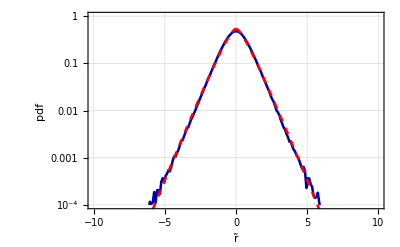

```mathematica
Show[ListLogPlot[Transpose[{xbins,hbins}],Joined->True,PlotRange->{{-10,10},{10^-4,1}},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],{16}], FrameLabel->{OverTilde[r],"pdf"}],LogPlot[kDistribution[R,3.2,1],{R,-10,10},PlotStyle->{Red,Dashed,Thickness[0.0045]}],ImageSize->Full,GridLines->Automatic
]
```

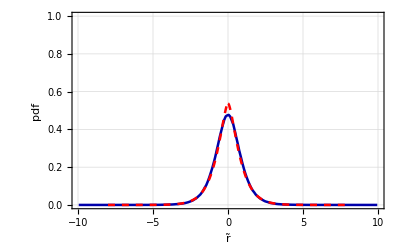

```mathematica
Show[ListPlot[Transpose[{xbins,hbins}],Joined->True,PlotRange->{{-10,10},{0,1}},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],{16}], FrameLabel->{OverTilde[r],"pdf"}],
Plot[kDistribution[R,3.2,1],{R,-8,8},PlotStyle->{Red,Dashed,Thickness[0.0045]},PlotRange->{{-10,10}, {0,1}}],ImageSize->Full,GridLines->Automatic
]
```

```mathematica
Manipulate[Show[ListPlot[Transpose[{xbins,hbins}],Joined->True,PlotRange->{{-10,10},All},PlotStyle->{Directive[Darker[Blue],Thickness[0.0045]]},Frame->True,FrameStyle->Directive[Thickness[0.0025],14], FrameLabel->{"rotated and rescaled returns","pdf"}],
Plot[kDistribution[R,M,1],{R,-10,10},PlotStyle->{Red,Dashed,Thickness[0.0045]},PlotRange->All],ImageSize->Full,GridLines->Automatic
],
{M,1,20,0.1}]
```

#### Check operations in Rotate_And_Scale function

```mathematica
Cov=Covariance@DailyReturnsT;
Dimensions@Cov
```

{352,352}

```mathematica
eigVal=Eigenvalues@Cov;
Dimensions@eigVal
eigVec=Eigenvectors@Cov;
Dimensions@eigVec
```

{352}

{352,352}

```mathematica
scale=DiagonalMatrix@(1/Sqrt[eigVal]);
Dimensions@scale
Rot=eigVec;
Dimensions@Rot
```

{352,352}

{352,352}

```mathematica
Dimensions@Map[(scale.Rot.#)&,DailyReturnsT]
```

{4851,352}

```mathematica
Dimensions[scale.Rot]
```

{352,352}

```mathematica
scale.Rot
```

{{-0.177028,-0.250377,-0.178802,-0.166778,-0.22127,-0.194722,-0.158658,-0.254969,336,-0.107364,-0.118414,-0.117472,-0.104989,-0.077264,-0.133473,-0.0875849,-0.106512},351}
 |  |  |  |

```mathematica
rotret = Map[(scale.Rot.#)&,DailyReturnsT]
```

{{0.139463,-0.131148,-0.0658958,-0.557259,-0.648759,0.446396,-0.280311,0.139332,336,1.55642,-0.159418,-0.0848972,1.25925,-0.397442,1.59223,-2.47107,-0.401606},4849,{1}}
 |  |  |  |

```mathematica
Dimensions@rotret
```

{4851,352}